```mathematica
FullSimplify[Normalize[{a-x,a^2-x^2}].Normalize[{1,2x}],{x,a}∈Reals]
```

((a-x) (1+2 x (a+x)))/(√((a-x)^2 (1+4 x^2) (1+(a+x)^2)))

```mathematica
FullSimplify[Normalize[{a-x,b-x^2}].Normalize[{1,2x}],{x,a,b}∈Reals]
```

(a+x (-1+2 b-2 x^2))/(√((1+4 x^2) ((a-x)^2+(b-x^2)^2)))

```mathematica
FullSimplify[Normalize[{a-x,b-x^2}].Normalize[{1,2x}],{x,a,b}∈Reals]/.{a->1,b->2}
```

(1+x (3-2 x^2))/(√((1+4 x^2) ((1-x)^2+(2-x^2)^2)))

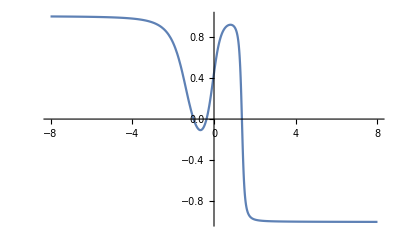

```mathematica
Plot[(1+x (3-2 x^2))/(√((1+4 x^2) ((1-x)^2+(2-x^2)^2))),{x,-8,8}]
```

```mathematica
1/x
```

1/x

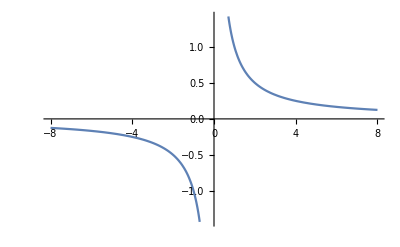

```mathematica
Plot[1/x,{x,-8,8}]
```

```mathematica
Limit[(1+x (3-2 x^2))/(√((1+4 x^2) ((1-x)^2+(2-x^2)^2))),x->1]
```

2/(√5)

```mathematica
Limit[(1+x (3-2 x^2))/(√((1+4 x^2) ((1-x)^2+(2-x^2)^2))),x->∞]
```

-1

```mathematica
Limit[(1+x (3-2 x^2))/(√((1+4 x^2) ((1-x)^2+(2-x^2)^2))),x->-∞]
```

1

```mathematica
FullSimplify[Normalize[{a-x,b-x^2}].,{x,a,b}∈Reals]
```